## Tracking a ramp (triangle wave input) (Example 3.7)

```mathematica
Clear["Global`*"]
```

```mathematica
G0 = 1/(1+s);K1 = 1/s;T0 =(G0 K1)/(1+G0 K1) // Simplify
```

1/(1+s+s^2)

```mathematica
K2 =(1+ s)^2/s^2
```

(1+s)^2/s^2

Note : K2 = (1+10 s^2) works even better as a controller (much less overshoot at corners).  However, it would require larger
inputs, which may not be feasible.  Also, it is bad to require an exact triangle wave for a physical stage, as that implies that
the velocity is reversed instantaneously.  Better to ask for a rounded triangle, with a max. acceleration that is feasible.

```mathematica
T1 = (G0 K2)/(1+G0 K2) // Simplify
```

(1+s)/(1+s+s^2)

```mathematica
u1 = K2/(1+G0 K2)// Simplify
```

(1+s)^2/(1+s+s^2)

```mathematica
K2a = (1+ 10s)^2/s^2
```

(1+10 s)^2/s^2

```mathematica
T2 = (G0 K2a)/(1+G0 K2a) // Simplify
```

(1+10 s)^2/(1+20 s+101 s^2+s^3)

can also look at the output of the controller :

```mathematica
u2 =  K2a/(1+G0 K2a) // Simplify
```

((1+s) (1+10 s)^2)/(1+20 s+101 s^2+s^3)

```mathematica
OutputResponse[TransferFunctionModel[T0,s],TriangleWave[t/20],{t,30}];
```

```mathematica
p1=Plot[{%,TriangleWave[t/20]},{t,0,30},PlotRange->Full];
```

```mathematica
OutputResponse[TransferFunctionModel[{T1,u1},s],TriangleWave[t/20],{t,30}];
```

```mathematica
p2=Plot[{%,TriangleWave[t/20]},{t,0,30},PlotRange->Full];
```

```mathematica
OutputResponse[TransferFunctionModel[{T2,u2},s],TriangleWave[t/20],{t,30}];
```

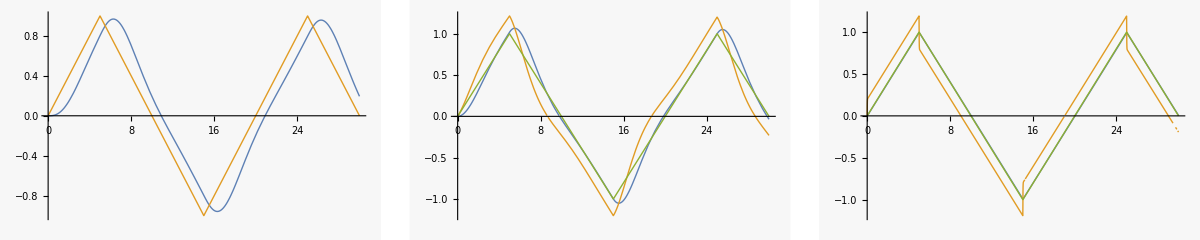

```mathematica
p3=Plot[{%,TriangleWave[t/20]},{t,0,30},PlotRange->Full];
GraphicsRow[{p1,p2,p3}]
```

```mathematica
{StateSpaceModel[TransferFunctionModel[T0,s]],
StateSpaceModel[TransferFunctionModel[T1,s]],
StateSpaceModel[TransferFunctionModel[T2,s]]}
```

{010-1-11100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,010-1-11110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,01000010-1-20-10111201000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}